```mathematica
Quit[]
```

# A pedagogical example

Here we are going to show the potentialities of the package SeaSyde` by solving the differential equation presented in eq. (1) in arXiv:2205.03345.

### Import the package and define the differential equation

```mathematica
SetDirectory[NotebookDirectory[]];
<<../SeaSyde.m
```

+++++ SeaSyde` +++++
Version 1.1.0

SeaSyde is a package for solving the system of differential equation associated to the Master Integrals of a given topology.

For any question or comment, please contact: 
[T. Armadillo](mailto:tommaso.armadillo@uclouvain.be), [R. Bonciani](mailto:roberto.bonciani@roma1.infn.it), [S. Devoto](mailto:simone.devoto@unimi.it), [N. Rana](mailto:narayan.rana@unimi.it) or [A. Vicini](mailto:alessandro.vicini@mi.infn.it).

For the latest version please see the [GitHub repository](https://github.com/TommasoArmadillo/SeaSyde).

```mathematica
Equation={f'[x]+1/(x^2-4x+5)f[x]==1/(x+2)};
BoundaryCondition= {f[0]==1};

MasterIntegral={f[x]};
PointBC={0};
```

### Configure and setup the package

```mathematica
Configuration={
EpsilonOrder->0,
ExpansionOrder->50
};
UpdateConfiguration[Configuration]
SetSystemOfDifferentialEquation[Equation,BoundaryCondition,MasterIntegral,{x+I δ},PointBC]
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 0

SeaSyde: Updated ExpansionOrder parameter, new value -> 50

SeaSyde: There are 1 kinematics variables {x}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ}

SeaSyde: There are 1 Master Integrals

SeaSyde: The boundary conditions are imposed in x==0.

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 1 equations and 1 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x} are respectively {{-2.,2.-1. ⅈ,2.+1. ⅈ}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

### Solving the differential equation

We can solve the equation in the point where the boundary conditions are imposed, e.g. x=0.

```mathematica
SolveSystem[x]
```

Solving equation for ϵ order 0

I solved the system of equation. The error estimate is: 5.51672×10^-17.

We can compare the first few terms with the exact result provided in eq. (3), (4) and (5).

```mathematica
ExactResult=1/2 x-7/40 x^2+2/75 x^3+1/5(5-x-3/10 x^2-11/150 x^3)//Expand//N
```

1.+0.3 x-0.235 x^2+0.012 x^3

```mathematica
Solution[]/.x^b_/;b>3->0//N
```

{1.+0.3 x-0.235 x^2+0.012 x^3}

The singularities are in x=-2, x=2±ⅈ. The closest to the centre of the series, x=0, is x=-2, hence the radius of convergence is ρ=|-2-0|=2. We can see that explicitly by plotting the solution along the real axes.

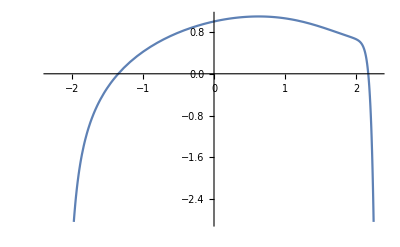

```mathematica
Plot[Solution[],{x,-2.3,2.3}]
```

If we go over x=2 the solution does not converge anymore.

### Extending the solution

If we want the solution in another point, e.g. x=-1+0.5ⅈ, we can attach multiple series solutions.

SeaSyde: Moving following these points: {0.,-1.+0.5 ⅈ}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

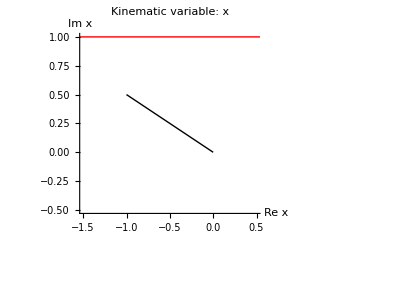

SeaSyde: Moving from the point x=0. to x=-1.+0.5 ⅈ, along the line x=(-1.+0.5 ⅈ) tInt

SeaSyde: The new point is: x=-0.894427+0.447214 ⅈ

SeaSyde: I arrived at x=-1.+0.5 ⅈ. The error estimate is: 5.51672×10^-17.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
TransportBoundaryConditions[{-1+0.5ⅈ}]
```

And we can access the value of the solution in x=-1+0.5ⅈ by using the SolutionValue[] method.

```mathematica
SolutionValue[]//N
```

{0.545912+0.443234 ⅈ}

### Crossing a branch-cut

We might want to overcome a branch-cut. In order to do so it is important to circumvent the singularities to the right

SeaSyde: There are 1 kinematics variables {x}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ}

SeaSyde: There are 1 Master Integrals

SeaSyde: The boundary conditions are imposed in x==0.

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 1 equations and 1 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x} are respectively {{-2.,2.-1. ⅈ,2.+1. ⅈ}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {0.,2.5,2.5+2. ⅈ,0.+2. ⅈ}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

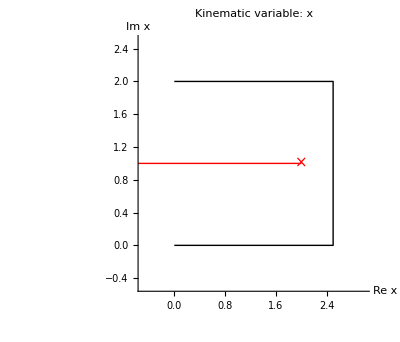

SeaSyde: Moving from the point x=0. to x=2.5, along the line x=2.5 tInt

SeaSyde: The new point is: x=1.

SeaSyde: The new point is: x=1.70711

SeaSyde: The new point is: x=2.22811

SeaSyde: Moving from the point x=2.5 to x=2.5+2. ⅈ, along the line x=2.5+(0.+2. ⅈ) tInt

SeaSyde: The new point is: x=2.5+0.559017 ⅈ

SeaSyde: The new point is: x=2.5+0.892358 ⅈ

SeaSyde: The new point is: x=2.5+1.14809 ⅈ

SeaSyde: The new point is: x=2.5+1.40882 ⅈ

SeaSyde: The new point is: x=2.5+1.73175 ⅈ

SeaSyde: Moving from the point x=2.5+2. ⅈ to x=0.+2. ⅈ, along the line x=(2.5+2. ⅈ)-2.5 tInt

SeaSyde: The new point is: x=1.94098+2. ⅈ

SeaSyde: The new point is: x=1.44011+2. ⅈ

SeaSyde: The new point is: x=0.867079+2. ⅈ

SeaSyde: The new point is: x=0.111514+2. ⅈ

SeaSyde: I arrived at x=0.+2. ⅈ. The error estimate is: 5.10206×10^-18.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
SetSystemOfDifferentialEquation[Equation,BoundaryCondition,MasterIntegral,{x+I δ},PointBC]
TransportVariable[x,2ⅈ]
```

```mathematica
SolutionValue[]//N
```

{-0.424527+0.399169 ⅈ}

If we cross the branch-cut directly, the result might be different

SeaSyde: There are 1 kinematics variables {x}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ}

SeaSyde: There are 1 Master Integrals

SeaSyde: The boundary conditions are imposed in x==0.

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 1 equations and 1 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x} are respectively {{-2.,2.-1. ⅈ,2.+1. ⅈ}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {0.,0.+2. ⅈ}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

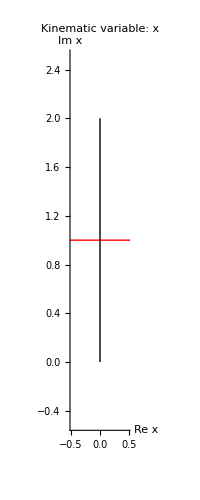

SeaSyde: Moving from the point x=0. to x=0.+2. ⅈ, along the line x=(0.+2. ⅈ) tInt

SeaSyde: The new point is: x=0.+1. ⅈ

SeaSyde: The new point is: x=0.+2. ⅈ

SeaSyde: I arrived at x=0.+2. ⅈ. The error estimate is: 1.1808×10^-16.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
SetSystemOfDifferentialEquation[Equation,BoundaryCondition,MasterIntegral,{x+I δ},PointBC]
TransportVariable[x,2ⅈ,CreateLine[{0,2ⅈ}]]
```

```mathematica
SolutionValue[]//N
```

{1.66537+0.582592 ⅈ}

We observe that the solution is different from the previous case. This is because by crossing the cut directly, we end up on another Riemann sheet.

### Examples of path

If we move on the real axes, it is important to give the right δ-prescription, in order to decide wether to pass above or under the singularity.

SeaSyde: Updated EpsilonOrder parameter, new value -> 0

SeaSyde: Updated ExpansionOrder parameter, new value -> 50

SeaSyde: There are 1 kinematics variables {x}

SeaSyde: The Feynman prescriptions for the variables are {ⅈ δ}

SeaSyde: There are 1 Master Integrals

SeaSyde: The boundary conditions are imposed in x==0.

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 1 equations and 1 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x} are respectively {{-2.,2.-1. ⅈ,2.+1. ⅈ}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {0.,0.+0.5 ⅈ,-4.+0.5 ⅈ,-4.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

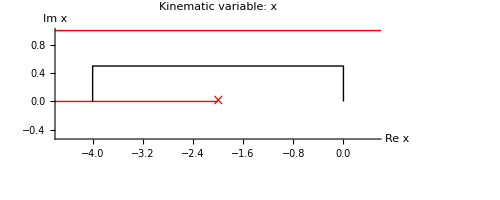

SeaSyde: Moving from the point x=0. to x=0.+0.5 ⅈ, along the line x=(0.+0.5 ⅈ) tInt

SeaSyde: Moving from the point x=0.+0.5 ⅈ to x=-4.+0.5 ⅈ, along the line x=(0.+0.5 ⅈ)-4. tInt

SeaSyde: The new point is: x=-1.03078+0.5 ⅈ

SeaSyde: The new point is: x=-1.57607+0.5 ⅈ

SeaSyde: The new point is: x=-1.90384+0.5 ⅈ

SeaSyde: The new point is: x=-2.15842+0.5 ⅈ

SeaSyde: The new point is: x=-2.42067+0.5 ⅈ

SeaSyde: The new point is: x=-2.74738+0.5 ⅈ

SeaSyde: The new point is: x=-3.19698+0.5 ⅈ

SeaSyde: The new point is: x=-3.84559+0.5 ⅈ

SeaSyde: Moving from the point x=-4.+0.5 ⅈ to x=-4., along the line x=(-4.+0.5 ⅈ)-(0.+0.5 ⅈ) tInt

SeaSyde: I arrived at x=-4.. The error estimate is: 1.27708×10^-16.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

The value of the solution is: {1.0654 + 3.40267 I}

```mathematica
Configuration={
EpsilonOrder->0,
ExpansionOrder->50
};
UpdateConfiguration[Configuration]
SetSystemOfDifferentialEquation[Equation,BoundaryCondition,MasterIntegral,{x+I δ},PointBC]
TransportVariable[x,-4]
Print[Style["The value of the solution is: "<>ToString[SolutionValue[]//N],Red]];
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 0

SeaSyde: Updated ExpansionOrder parameter, new value -> 50

SeaSyde: There are 1 kinematics variables {x}

SeaSyde: The Feynman prescriptions for the variables are {-ⅈ δ}

SeaSyde: There are 1 Master Integrals

SeaSyde: The boundary conditions are imposed in x==0.

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 1 equations and 1 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x} are respectively {{-2.,2.-1. ⅈ,2.+1. ⅈ}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

SeaSyde: Moving following these points: {0.,0.-0.5 ⅈ,-4.-0.5 ⅈ,-4.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

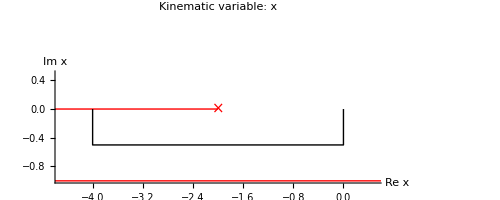

SeaSyde: Moving from the point x=0. to x=0.-0.5 ⅈ, along the line x=(0.-0.5 ⅈ) tInt

SeaSyde: Moving from the point x=0.-0.5 ⅈ to x=-4.-0.5 ⅈ, along the line x=(0.-0.5 ⅈ)-4. tInt

SeaSyde: The new point is: x=-1.03078-0.5 ⅈ

SeaSyde: The new point is: x=-1.57607-0.5 ⅈ

SeaSyde: The new point is: x=-1.90384-0.5 ⅈ

SeaSyde: The new point is: x=-2.15842-0.5 ⅈ

SeaSyde: The new point is: x=-2.42067-0.5 ⅈ

SeaSyde: The new point is: x=-2.74738-0.5 ⅈ

SeaSyde: The new point is: x=-3.19698-0.5 ⅈ

SeaSyde: The new point is: x=-3.84559-0.5 ⅈ

SeaSyde: Moving from the point x=-4.-0.5 ⅈ to x=-4., along the line x=(-4.-0.5 ⅈ)+(0.+0.5 ⅈ) tInt

SeaSyde: I arrived at x=-4.. The error estimate is: 1.27708×10^-16.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

The value of the solution is: {1.0654 - 3.40267 I}

```mathematica
Configuration={
EpsilonOrder->0,
ExpansionOrder->50
};
UpdateConfiguration[Configuration]
SetSystemOfDifferentialEquation[Equation,BoundaryCondition,MasterIntegral,{x-I δ},PointBC]
TransportVariable[x,-4]
Print[Style["The value of the solution is: "<>ToString[SolutionValue[]//N],Red]];
```

And we can note that the imaginary part has an opposite sign.